```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/souda/Documents/Projects/CHASE/Jerry-Meyer-Reorganization-energy

## Unit conversion factors

```mathematica
C2K[TC_]:=QuantityMagnitude@UnitConvert[Quantity[TC,"DegreesCelsius"],"Kelvins"];
K2C[TK_]:=QuantityMagnitude@UnitConvert[Quantity[TK,"Kelvins"],"DegreesCelsius"];
C2F[TC_]:=QuantityMagnitude@UnitConvert[Quantity[TC,"DegreesCelsius"],"DegreesFarenheit"];
F2C[TF_]:=QuantityMagnitude@UnitConvert[Quantity[TF,"DegreesFarenheit"],"DegreesCelsius"];
```

```mathematica
bohr2a=QuantityMagnitude@UnitConvert[Quantity[1,"BohrRadius"],"Angstroms"];
a2bohr=1/bohr2a;
au2kcal=QuantityMagnitude[UnitConvert[Quantity[1,"Hartrees"],"kilocalories"]×Entity["PhysicalConstant","AvogadroConstant"]["Value"]];
kcal2au=1/au2kcal;
ev2kcal=QuantityMagnitude[UnitConvert[Quantity[1,"ElectronVolts"],"kilocalories"]×Entity["PhysicalConstant","AvogadroConstant"]["Value"]];
kcal2ev=1/ev2kcal;
ev2cm=QuantityMagnitude@UnitConvert[Quantity[1,"ElectronVolts"]/(Entity["PhysicalConstant","PlanckConstant"]["Value"]×Entity["PhysicalConstant","SpeedOfLight"]["Value"]),"wavenumbers"];
cm2ev=1/ev2cm;
au2ev=QuantityMagnitude@UnitConvert[Quantity[1,"Hartrees"],"ElectronVolts"];
ev2au=1/au2ev;
au2cm=QuantityMagnitude@UnitConvert[Quantity[1,"Hartrees"]/(Entity["PhysicalConstant","PlanckConstant"]["Value"]×Entity["PhysicalConstant","SpeedOfLight"]["Value"]),"wavenumbers"];
cm2au=1/au2cm;
a2m=10^-10;
m2a=1/a2m;
m2bohr=m2a a2bohr;
bohr2m=1/m2bohr;
debye2SI=QuantityMagnitude@UnitConvert[Quantity[1,"Debyes"],"Coulomb"*"Meters"];
debye2au=QuantityMagnitude@UnitConvert[Quantity[1,"Debyes"],"ElementaryCharge"*"BohrRadius"];
```

## Universal constants

```mathematica
ℏ=1; (* in atomic units *)
hbar=QuantityMagnitude@Entity["PhysicalConstant","ReducedPlanckConstant"]["Value"]; (* in Joule × seconds *)
Dalton=QuantityMagnitude@UnitConvert[1 Quantity[, "Daltons"],"electronmass"];
μH=QuantityMagnitude@UnitConvert[Quantity[, "ProtonMass"],"electronmass"];
μD=QuantityMagnitude@UnitConvert[Quantity[, "DeuteronMass"],"electronmass"];
MassH=μH/Dalton;
MassD=μD/Dalton;
kb=QuantityMagnitude@UnitConvert[Entity["PhysicalConstant","BoltzmannConstant"]["Value"],"Hartrees/K"];
kB=QuantityMagnitude@Entity["PhysicalConstant","BoltzmannConstant"]["Value"];
NAvogadro=QuantityMagnitude@Entity["PhysicalConstant","AvogadroConstant"]["Value"];
R=kB×NAvogadro;
elcharge=QuantityMagnitude@Entity["PhysicalConstant","ElementaryCharge"]["Value"];
F=QuantityMagnitude@Entity["PhysicalConstant","FaradayConstant"]["Value"];
ε0=QuantityMagnitude@Entity["PhysicalConstant","ElectricConstant"]["Value"];
hbar=QuantityMagnitude@Entity["PhysicalConstant","ReducedPlanckConstant"]["Value"];
Debye=QuantityMagnitude@UnitConvert[Entity["PhysicalConstant","BoltzmannConstant"]["Value"],"Hartrees/K"];
```

## Chemical constants

kT at 300K in eV:

```mathematica
kTeV=kb 300 au2ev;
```

0.025851999786

## Experimental quantities

pKa’s:
Ru(III)-H_2 O → Ru(III)-OH^-
H_3 O^+ → H_2 O + H^+

```mathematica
pKaRuH2O=1.7;
pKaH3O=0;
```

Equlibrium potential (halfwave) for Ru(III)/Ru(II) pair (Volts vs. NHE):

```mathematica
Ehalf=1.09;
```

Reaction free energies:

```mathematica
ΔGET[Eapp_]:=Eapp-Ehalf;
ΔGPCET[Eapp_]:=Eapp-Ehalf+kTeV(pKaRuH2O-pKaH3O);
```

## Fit of the measured rate constant

```mathematica
khalfETscaled[λ_,Eapp_]:=1/2(1-Erf[(ΔGET[Eapp]+λ)/(2 √(λ kTeV))]);
```

```mathematica
khalfPCETscaled[λ_,Eapp_,W_]:=1/2(1-Erf[(ΔGPCET[Eapp]+W+λ)/(2 √(λ kTeV))]);
```

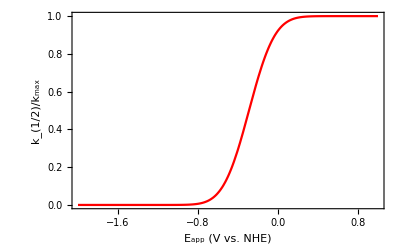

```mathematica
Plot[{khalfETscaled[0.8,-Eapp]},{Eapp,-2,1},
Axes->False,Frame->True,
PlotStyle->{Red},
FrameLabel->{"E_app (V vs. NHE)","k_(1/2)/k_max"}]
```

```mathematica
khalfPCETscaledR[λ_,Eapp_,R_]:=1/2(1-Erf[(ΔGPCET[Eapp]+W[R]+λR[R])/(2 √(λ kTeV))]);
```